This notebook contains the code and data necessary to evaluate the Figures.nb and SupplementalFigures.nb notebooks for the paper “Situating the actual within the space of the possible: Parameter space structure and degeneracy in brain-body-environment systems” by Randall D. Beer and Eduardo J. Izquierdo.

To use, simply evaluate all of the cells in this file before evaluating any cells in “Figures.nb” or “SupplementalFigures.nb” files.

Randall D. Beer - 7/1/2025

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
LaunchKernels[];
```

```mathematica
ParallelEvaluate[Block[{Print=Identity},<<"Dynamica.m"]];
```

### General

```mathematica
$MaxFitness=N[165/(85Sqrt[6]+8Sqrt[15π])]
```

0.627081

```mathematica
ParameterRanges[data_]:=
{Map[{Floor[#[[1]]],Ceiling[#[[2]]]}&,Table[MinMax[#[[i]]&/@Select[data,#[[4]]<0&]],{i,1,8}]],
Map[{Floor[#[[1]]],Ceiling[#[[2]]]}&,Table[MinMax[#[[i]]&/@Select[data,#[[4]]>0&]],{i,1,8}]]}
```

```mathematica
SanitizeAndReEvaluateData[data_,cutoff_]:=
Select[
ParallelMap[
Append[Drop[#,-1],CAsymptoticFitness[Thread[{θ1,θ2,w11,w21,w12,w22,τ1,τ2}->Drop[#,-1]],250,10,0.005]]&,
Select[data,Cases[#,e,∞]==={}&&NoneTrue[#,Head[#]===Times&]&]],
Last[#]>=cutoff&]
```

```mathematica
ZeroCrossings[l_]:=SparseArray[#]["AdjacencyLists"]&/. SApos_:>With[{c=SApos[l]},{c[[#]],c[[#+1]]}ᵀ&@SApos@Differences@Sign@l[[c]]]
```

### CTRNN Model

```mathematica
Pis={w11->15.954491095680044310256562312134,w12->11.170298542740031422226820723154,w21->-11.952550559109566208348951477092,w22->12.816995425769682981353980721906,θ1->-3.2092214155564793287567226798274,θ2->-13.727075396871940782261845015455,τ1->0.54981014585212317768991852062754,τ2->8.1354350786053615252058079931885};
```

```mathematica
σ[x_]=1/(1+ⅇ^-x);
```

```mathematica
DS=
DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2])/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-50,50},{y2,-50,50}},
{{w11,-24,24},{w12,-24,24},{w21,-24,24},{w22,-24,24},{θ1,-24,24},{θ2,-24,24},{τ1,0.05,10},{τ2,0.05,10}}];
```

```mathematica
DS=DS/.Pis;
```

```mathematica
With[{ε=0.0001},
DSo=TransformDynamicalSystem[DS,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
```

```mathematica
IL[w_]:=2Log[(√w+√(w-4))/2]-(w+√(w(w-4)))/2;
IR[w_]:=-2Log[(√w+√(w-4))/2]-(w-√(w(w-4)))/2;
IW[w_] :=√(w(w-4))- 4Log[(√w+√(w-4))/2]
OverTilde[IL][w_]:=If[w<4,-2,IL[w]]
OverTilde[IR][w_]:=If[w<4,2-w,IR[w]]
OverTilde[IW][w_]:=If[w<4,4-w,IR[w]-IL[w]]
ILInv[x_?NumberQ]:=InverseFunction[2Log[(√#+√(#-4))/2]-(#+√(#(#-4)))/2&][x];
IRInv[x_?NumberQ]:=InverseFunction[-2Log[(√#+√(#-4))/2]-(#-√(#(#-4)))/2&][x];
```

```mathematica
DisplaySSIODiagram[ws_?NumberQ,wc_?NumberQ,θ_?NumberQ]:=
Module[{L=IL[ws]-θ,R=IR[ws]-θ},
ContourPlot[o(1-o)(ws o - Log[o/(1-o)]+θ+J)==0,{J,-15,15},{o,0.0000000000001,0.999999999999},
PlotPoints->250,PlotRange->{{-15,15},Automatic},
FrameLabel->{"I",o}(*,
Prolog->{LightGray,Rectangle[{wc,0},{0,1}]},*)
(*Epilog->{Dashed,Red,Line[{{L,0},{L,1}}],Darker[Green],Line[{{R,0},{R,1}}]}*)]]
```

### C Body Model

```mathematica
Needs["CCompilerDriver`"]

If[StringQ[lib],LibraryUnload[lib]];
lib=CreateLibrary["
#include \"WolframLibrary.h\"
#include <math.h>
#include <fstream>
#include <vector>

// Global Constants
const double Pi = 3.14159265358979323846264338327950288582;
const double MaxPeriod = 1000;

// Default CPG Parameters
double Theta1 = -3.2092214155564793287567226798274, Theta2 = -13.727075396871940782261845015455;
double Tau1 = 0.54981014585212317768991852062754, Tau2 = 8.1354350786053615252058079931885;
double W11 = 15.954491095680044310256562312134, W21 = -11.952550559109566208348951477092; 
double W12 = 11.170298542740031422226820723154, W22 = 12.816995425769682981353980721906;

// Body Constants
const int    LegLength = 15;
const double MaxLegForce = 0.05;
const double ForwardAngleLimit = Pi/6;
const double BackwardAngleLimit = -Pi/6;
const double MaxVelocity = 6.0;
const double MaxTorque = 0.5;
const double MaxOmega = 1.0;

// Global CPG Variables
double z1, z2;
double o1, o2;
enum state {StancePower,StanceCoast,StanceFreeze,Swing,SwingFreeze} S;

// Global Body Variables
double cx, cy;
double vx;
double JointX, JointY, FootX, FootY;
double Angle, Omega;
int    FootState;
double ForwardForce, BackwardForce, f = 0.0;

// The sigmoid function
double sigma(double x) 
{
  return 1/(1 + exp(-x));
}

// Reset everything
void Reset()
{
  cx = 0; cy = 0; vx = 0;
  FootState = 0;
  Angle = ForwardAngleLimit;
  Omega = ForwardForce = BackwardForce = 0.0;
  JointX = cx; JointY = cy + 12.5;
  FootX = JointX + LegLength * sin(Angle);
  FootY = JointY + LegLength * cos(Angle);
  z1 = z2 = 0;
  o1 = sigma(z1 + Theta1);
  o2 = sigma(z2 + Theta2);
}

// Step the walker using a CPG with only 1 motor neuron

void StepCPG(double StepSize)
{
  double force = 0.0;

  // Update the nervous system
  z1 += StepSize * (1/Tau1) * (W11 * o1 + W21 * o2 - z1);
  z2 += StepSize * (1/Tau2) * (W12 * o1 + W22 * o2 - z2);
  o1 = sigma(z1 + Theta1);
  o2 = sigma(z2 + Theta2);

  // Update the leg effectors
  if (o1 > 0.5) {
    FootState = 1;
    Omega = 0;
	ForwardForce = 2 * (o1 - 0.5) * MaxLegForce;
    BackwardForce = 0;
  }
  else {
	FootState = 0;
    ForwardForce = 0;
	BackwardForce = 2 * (0.5 - o1) * MaxLegForce;
  }

  // Compute the force applied to the body 
  double f = ForwardForce - BackwardForce;
  if (FootState == 1) 
    if ((Angle >= BackwardAngleLimit && Angle <= ForwardAngleLimit)||
        (Angle < BackwardAngleLimit && f < 0)||
        (Angle > ForwardAngleLimit && f > 0)) 
      force = f;

  // Update the position of the body 
  vx = vx + StepSize * force;
  if (vx < -MaxVelocity) vx = -MaxVelocity;
  if (vx > MaxVelocity) vx = MaxVelocity;
  cx = cx + StepSize*vx;

 // Update the leg geometry 
 JointX = JointX + StepSize * vx;
 if (FootState == 1) {
   double angle = atan2(FootX - JointX, FootY - JointY);
   Omega = (angle - Angle)/StepSize;
   Angle = angle;
  } 
  else {
    vx = 0.0;
    Omega =  Omega + StepSize * MaxTorque * (BackwardForce - ForwardForce);
    if (Omega < -MaxOmega) Omega = -MaxOmega;
    if (Omega > MaxOmega) Omega = MaxOmega;
    Angle = Angle + StepSize * Omega;
    if (Angle < BackwardAngleLimit) {Angle = BackwardAngleLimit; Omega = 0;} 
    if (Angle > ForwardAngleLimit) {Angle = ForwardAngleLimit; Omega = 0;} 
    FootX = JointX + LegLength*sin(Angle);
    FootY = JointY + LegLength*cos(Angle);
  }

  // If the foot is too far back,the body becomes unstable and forward motion ceases 
  if (cx-FootX > 20) vx = 0.0;
}

/*
void StepCPG(double StepSize)
{
  // Update the nervous system
  z1 += StepSize * (1/Tau1) * (W11 * o1 + W21 * o2 - z1);
  z2 += StepSize * (1/Tau2) * (W12 * o1 + W22 * o2 - z2);
  o1 = sigma(z1 + Theta1);
  o2 = sigma(z2 + Theta2);

  if (o1 > 0.5) {
    // Foot down
    S = StancePower;
    FootState = 1;
    Omega = 0;
    double Force = 2 * (o1 - 0.5) * MaxLegForce;
    // Force can only be applied to the body under certain conditions
    if ((Angle >= BackwardAngleLimit && Angle <= ForwardAngleLimit)||
        (Angle < BackwardAngleLimit && Force < 0)||
        (Angle > ForwardAngleLimit && Force > 0)) 
      vx += StepSize * Force;
    else S = StanceCoast;
    cx += StepSize*vx;
    // Update ANGLE and OMEGA from body and foot positions
    JointX = JointX + StepSize * vx;
    double angle = atan2(FootX - JointX, FootY - JointY);
    Omega = (angle - Angle)/StepSize;
    Angle = angle;
    // Check that leg remains within absolute angle limits
    if (cx-FootX > 20) {S = StanceFreeze; vx = 0.0;}
  }
  else {
    // Foot up
	S = Swing;
	FootState = 0;
    vx = 0;
    double Alpha = MaxTorque * 2 * (0.5 - o1) * MaxLegForce;
    Omega += StepSize * Alpha;
    Angle += StepSize * Omega;
    // Check that leg remains within angle limits
    if (Angle < BackwardAngleLimit) {S = SwingFreeze; Angle = BackwardAngleLimit; Omega = 0;} 
    if (Angle > ForwardAngleLimit) {S = SwingFreeze; Angle = ForwardAngleLimit; Omega = 0;} 
    // Update foot position from ANGLE
    FootX = JointX + LegLength*sin(Angle);
    FootY = JointY + LegLength*cos(Angle);
  }
}
*/
/*
void StepCPG(double StepSize)
{
  // Update the nervous system
  z1 += StepSize * (1/Tau1) * (W11 * o1 + W21 * o2 - z1);
  z2 += StepSize * (1/Tau2) * (W12 * o1 + W22 * o2 - z2);
  o1 = sigma(z1 + Theta1);
  o2 = sigma(z2 + Theta2);

  // Update the body
  if (o1 > 0.5) {
    // Foot down
    if (FootState == 0) {
	  Angle = fmax(fmin(Angle, ForwardAngleLimit), BackwardAngleLimit);
      FootX = JointX + LegLength*sin(Angle);
      FootY = JointY + LegLength*cos(Angle);
    }
    FootState = 1;
    Omega = 0;
    // Check that leg remains within absolute angle limits
    if (cx-FootX > 20) {
      S = StanceFreeze;
      vx = 0.0;
    }
    else {
      // Force can only be applied to the body when leg is within angle limits
      if (Angle < BackwardAngleLimit || Angle > ForwardAngleLimit) {
        S = StanceCoast;
        cx += StepSize * vx;
      }
      else {
        S = StancePower;
        vx += StepSize * 2 * (o1 - 0.5) * MaxLegForce;
        cx += StepSize * vx;
      }
    }
    // Update ANGLE and OMEGA from body and foot positions
    JointX = JointX + StepSize * vx;
    double angle = atan2(FootX - JointX, FootY - JointY);
    Omega = (angle - Angle)/StepSize;
    Angle = angle;
  }
  else {
    // Foot up
    if (FootState == 1) Angle = fmax(fmin(Angle, ForwardAngleLimit), BackwardAngleLimit);
	FootState = 0;
    vx = 0;
    if (Angle < BackwardAngleLimit || Angle > ForwardAngleLimit) {
      S = SwingFreeze;
      Omega = 0;
    }
    else {
      S = Swing;
      Omega += StepSize * MaxTorque * 2 * (0.5 - o1) * MaxLegForce;
      Angle += StepSize * Omega;
    }
    //Angle = fmax(fmin(Angle, ForwardAngleLimit), BackwardAngleLimit);
    // Update foot position from ANGLE
    FootX = JointX + LegLength*sin(Angle);
    FootY = JointY + LegLength*cos(Angle);
    }
}
*/

int FindStanceBegin(double TransientDuration, double StepSize)
{
  double time = 0, period = 0;
  int oldFootState;

  // Reset everything
  Reset();

  // Skip transients
  for (time = 0; time <= TransientDuration; time += StepSize) {
    oldFootState = FootState;
    StepCPG(StepSize);
  }

  // Run until the first foot down
  while (FootState <= oldFootState) {
	oldFootState = FootState;
    StepCPG(StepSize);
	time += StepSize;
    period += StepSize;
    if (period > MaxPeriod) return 0;
  }
  return 1;
}

double NewFindStanceBegin(double StepSize)
{
  double time = 0, period = 0;
  int oldFootState = FootState;

  // Run until the first foot down
  while (FootState <= oldFootState) {
	oldFootState = FootState;
    StepCPG(StepSize);
	time += StepSize;
    period += StepSize;
    if (period > MaxPeriod) return 0;
  }
return time;
}

double ComputeAsymptoticFitness(double TransientDuration, int SkipSteps, double StepSize)
{
  double time = 0, period = 0;

  // Reset everything
  Reset();

  // Skip transients
  for (time = 0; time <= TransientDuration; time += StepSize)
    StepCPG(StepSize);

  // Skip the specified number of steps
  for (int i = 1; i <= SkipSteps; i++) {
    period = NewFindStanceBegin(StepSize);
    if (period == 0) return 0;
  }

  //Run until the next foot down
  double startx = cx;
  period = NewFindStanceBegin(StepSize);
  if (period == 0) return 0;

  // Return velocity over one full step
  return((cx-startx)/period);
}

double ComputeTruncatedFitness(double Duration, double StepSize)
{
  // Reset everything
  Reset();

  // Run for the specified duration
  for (double time = 0; time <= Duration; time += StepSize) {
    StepCPG(StepSize);
  }

  // Return the average velocity
  return(cx/Duration);
}

// The Mathematica Interface
EXTERN_C DLLEXPORT int RunCPGTrajectory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
  double *TD = libData->MTensor_getRealData(MArgument_getMTensor(Args[0]));
  Tau1 = TD[0];
  Tau2 = TD[1];
  Theta1 = TD[2];
  Theta2 = TD[3];
  W11 = TD[4];
  W21 = TD[5];
  W12 = TD[6];
  W22 = TD[7];
  double Skip = MArgument_getReal(Args[1]);
  double Duration = MArgument_getReal(Args[2]);
  double StepSize = MArgument_getReal(Args[3]);
  double time;

  // Reset everything
  Reset();

  // Skip transients
  for (time = 0; time <= Skip; time += StepSize) {
    StepCPG(StepSize);
  }

  // Prepare MTensor
  MTensor T0;
  int steps = Duration/StepSize;
  mint dims[2]; dims[0] = steps; dims[1] = 8;
  int err = libData->MTensor_new(MType_Real, 2, dims, &T0);
  mint pos[2];

  // Run for the specified Duration, recording state into MTensor T0
  for (mint i = 1; i <= steps; i++)
  {
    pos[0] = i;
    pos[1] = 1; err = libData->MTensor_setReal(T0, pos, time);
    pos[1] = 2; err = libData->MTensor_setReal(T0, pos, z1);
    pos[1] = 3; err = libData->MTensor_setReal(T0, pos, z2);
    pos[1] = 4; err = libData->MTensor_setReal(T0, pos, Angle);
    pos[1] = 5; err = libData->MTensor_setReal(T0, pos, Omega);
    pos[1] = 6; err = libData->MTensor_setReal(T0, pos, cx);
    pos[1] = 7; err = libData->MTensor_setReal(T0, pos, vx);
    pos[1] = 8; err = libData->MTensor_setReal(T0, pos, S);
    StepCPG(StepSize);
	time += StepSize;
  }

// Return result
MArgument_setMTensor(Res, T0);
return err;
}

EXTERN_C DLLEXPORT int StepCycleTrajectory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res) 
{
  double *TD = libData->MTensor_getRealData(MArgument_getMTensor(Args[0]));
  Tau1 = TD[0];
  Tau2 = TD[1];
  Theta1 = TD[2];
  Theta2 = TD[3];
  W11 = TD[4];
  W21 = TD[5];
  W12 = TD[6];
  W22 = TD[7];
  double TransientSkip = MArgument_getReal(Args[1]);
  double StepSize = MArgument_getReal(Args[2]);

  // Skip the specified transients and then run until the next stance phase begins
  int flag = FindStanceBegin(TransientSkip, StepSize);
  if (flag == 0) return LIBRARY_FUNCTION_ERROR;

  // Run until the next foot down
  std::vector<double> vinit(5, 0);
  std::vector<std::vector<double> > T(0, vinit);
  double time = 0, period = 0;
  int oldFootState = FootState;
  // Save initial state
  int j = 0;
  T.push_back(vinit); T[j][0] = time; T[j][1] = z1; T[j][2] = z2; T[j][3] = Angle; T[j][4] = Omega;
  // Run until next foot down
  while (FootState <= oldFootState) {
	oldFootState = FootState;
    time += StepSize;
    StepCPG(StepSize);
    // Save current state
    T.push_back(vinit); j += 1; T[j][0] = time; T[j][1] = z1; T[j][2] = z2; T[j][3] = Angle; T[j][4] = Omega;
    period += StepSize;
    if (period > MaxPeriod) return LIBRARY_FUNCTION_ERROR;
  }

  // Allocate a rank-2 MTensor of the appropriate size and copy the state into it
  MTensor T0;
  mint dims[2]; dims[0] = T.size(); dims[1] = 5;
  int err = libData->MTensor_new(MType_Real, 2, dims, &T0);
  mint pos[2];
  for (mint i = 1; i <= T.size(); i++) {
    pos[0] = i;
    pos[1] = 1; err = libData->MTensor_setReal(T0, pos, T[i-1][0]);
    pos[1] = 2; err = libData->MTensor_setReal(T0, pos, T[i-1][1]);
    pos[1] = 3; err = libData->MTensor_setReal(T0, pos, T[i-1][2]);
    pos[1] = 4; err = libData->MTensor_setReal(T0, pos, T[i-1][3]);
    pos[1] = 5; err = libData->MTensor_setReal(T0, pos, T[i-1][4]);
  }
  MArgument_setMTensor(Res, T0);
  return err;
}

EXTERN_C DLLEXPORT int TruncatedFitness(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res) 
{
	double *TD = libData->MTensor_getRealData(MArgument_getMTensor(Args[0]));
    Tau1 = TD[0];
    Tau2 = TD[1];
	Theta1 = TD[2];
    Theta2 = TD[3];
    W11 = TD[4];
    W21 = TD[5];
    W12 = TD[6];
    W22 = TD[7];
	MArgument_setReal(Res, ComputeTruncatedFitness(MArgument_getReal(Args[1]), MArgument_getReal(Args[2])));
	return LIBRARY_NO_ERROR;
}

EXTERN_C DLLEXPORT int AsymptoticFitness(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res) 
{
	double *TD = libData->MTensor_getRealData(MArgument_getMTensor(Args[0]));
    Tau1 = TD[0];
    Tau2 = TD[1];
	Theta1 = TD[2];
    Theta2 = TD[3];
    W11 = TD[4];
    W21 = TD[5];
    W12 = TD[6];
    W22 = TD[7];
	double F = ComputeAsymptoticFitness(MArgument_getReal(Args[1]), MArgument_getInteger(Args[2]),MArgument_getReal(Args[3]));
	MArgument_setReal(Res, F);
	return LIBRARY_NO_ERROR;
}","WalkingFitness","Language"->"C++","ShellOutputFunction"->Identity,"ShellCommandFunction"->Identity];
CRunCPGTrajectoryInternal=LibraryFunctionLoad[lib,"RunCPGTrajectory",{{Real,1,"Constant"},Real,Real,Real},{Real,2}];
CTruncatedFitnessInternal=LibraryFunctionLoad[lib,"TruncatedFitness",{{Real,1,"Constant"},Real,Real},Real];
CAsymptoticFitnessInternal=LibraryFunctionLoad[lib,"AsymptoticFitness",{{Real,1,"Constant"},Real,Integer,Real},Real];
CStepCycleTrajectoryInternal=LibraryFunctionLoad[lib,"StepCycleTrajectory",{{Real,1,"Constant"},Real,Real},{Real,2}];

CRunCPGTrajectory[ParameterSubsts_:{},Skip_:220,Duration_:220,StepSize_:0.01]:=CRunCPGTrajectoryInternal[{τ1,τ2,θ1,θ2,w11,w21,w12,w22}/. ParameterSubsts/. Pis,Skip,Duration,StepSize]/;AllTrue[ParameterSubsts,MatchQ[#,_Symbol->_?NumberQ]&]&&NumberQ[Duration]&&NumberQ[StepSize]

CTruncatedFitness[ParameterSubsts_:{},Duration_:220,StepSize_:0.01]:=CTruncatedFitnessInternal[{τ1,τ2,θ1,θ2,w11,w21,w12,w22}/. ParameterSubsts/. Pis,Duration,StepSize]/;AllTrue[ParameterSubsts,MatchQ[#,_Symbol->_?NumberQ]&]&&NumberQ[Duration]&&NumberQ[StepSize]

CAsymptoticFitness[ParameterSubsts_:{},TransientDuration_:220,SkipSteps_:1,StepSize_:0.01]:=CAsymptoticFitnessInternal[{τ1,τ2,θ1,θ2,w11,w21,w12,w22}/. ParameterSubsts/. Pis,TransientDuration,SkipSteps,StepSize]/;AllTrue[ParameterSubsts,MatchQ[#,_Symbol->_?NumberQ]&]&&NumberQ[TransientDuration]&&NumberQ[StepSize]

CStepCycleTrajectory[ParameterSubsts_:{},TransientDuration_:220,StepSize_:0.01]:=Module[{result},result=CStepCycleTrajectoryInternal[{τ1,τ2,θ1,θ2,w11,w21,w12,w22}/. ParameterSubsts/. Pis,TransientDuration,StepSize];
If[!ListQ[result],$Failed,result]]/;AllTrue[ParameterSubsts,MatchQ[#,_Symbol->_?NumberQ]&]&&NumberQ[TransientDuration]&&NumberQ[StepSize]

DisplayCBodyCycle[ParameterSubsts_,skip_:220,duration_:250,step_:0.1]:=
Show[OG,ListPlot[{#[[4]],#[[5]]}&/@CRunCPGTrajectory[ParameterSubsts,skip,duration,step],PlotStyle->Directive[Orange,AbsoluteThickness[1]],Joined->True,PlotRange->All],AspectRatio->1,Frame->True,FrameStyle->Red,FrameTicks->None,Axes->False]
```

```mathematica
CGaitParameters[PSubs_:{},SkipDuration_:220,StepSize_:0.01]:=
Module[{L,is,Upis,Downis,ϕDown,ϕUp,T,ΔT,ϕMin},
L=CStepCycleTrajectory[PSubs,SkipDuration,StepSize];
If[L===$Failed,Return[{$Failed,$Failed,$Failed,$Failed}]];
L=Map[{#[[1]],σ[#[[2]]+θ1/.PSubs/.Pis],σ[#[[3]]+θ2/.PSubs/.Pis],#[[4]],#[[5]]}&,L];
T=Last[L][[1]];
ϕDown=L[[1,4]];
ϕUp=L[[First[FirstPosition[L,{_,o_,_,_,_}/;o<0.5]]-1,4]];
ϕMin=Min[Map[#[[4]]&,L]];
{ϕDown,ϕUp,T-TStar[ϕDown,ϕUp],ϕMin}
]
```

```mathematica
StepperQ[Θ1_?NumberQ,W11_?NumberQ,W21_?NumberQ,Skip_:1000,StepSize_:0.01]:=
CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},Skip,1,StepSize]>0
```

```mathematica
CBodyCycle[ParameterSubsts_,skip_:220,duration_:250,step_:0.1]:=
Module[{OG},
OG=Show[
ParametricPlot[{-ArcTan[(t^2-300)/(300 √3)],-(600t √3)/(t^4-600 t^2+360000)},{t,0,10 √6},PlotStyle->Directive[Green,Dashed,AbsoluteThickness[1.25]]],
ParametricPlot[{-ArcTan[(t √6+15)/(15 √3)],-15/(√2(t^2+5t √6+150))},{t,0,25/√6},PlotStyle->Directive[Green,Dashed,AbsoluteThickness[1.25]]],
ParametricPlot[{t^2/80-π/6,t/40},{t,0,4 √(5π/3)},PlotStyle->Directive[Green,Dashed,AbsoluteThickness[1.25]]],
Graphics[{Green,Dashed,AbsoluteThickness[1.25],Line[{{-ArcTan[8/(3 √3)],-(9 √2)/455},{-π/6,0}}],Line[{{π/6,(√(π/15))/2},{π/6,0}}]}],
PlotRange->All];
Show[
OG,
ListPlot[
{#[[4]],#[[5]]}&/@CRunCPGTrajectory[ParameterSubsts,skip,duration,step],
PlotStyle->Directive[Orange,AbsoluteThickness[1]],Joined->True,PlotRange->All],AspectRatio->1,Frame->True,FrameStyle->Red,FrameTicks->None,Axes->False]]
```

```mathematica
OG=Show[
ParametricPlot[{-ArcTan[(t^2-300)/(300 √3)],-(600t √3)/(t^4-600 t^2+360000)},{t,0,10 √6},PlotStyle->Directive[Gray,Dashed,AbsoluteThickness[1]]],
ParametricPlot[{-ArcTan[(t √6+15)/(15 √3)],-15/(√2(t^2+5t √6+150))},{t,0,25/√6},PlotStyle->Directive[Gray,Dashed,AbsoluteThickness[1]]],
ParametricPlot[{t^2/80-π/6,t/40},{t,0,4 √(5π/3)},PlotStyle->Directive[Gray,Dashed,AbsoluteThickness[1]]],
Graphics[{Gray,Dashed,AbsoluteThickness[1],Line[{{-ArcTan[8/(3 √3)],-(9 √2)/455},{-π/6,0}}],Line[{{π/6,(√(π/15))/2},{π/6,0}}]}],
PlotRange->All,Axes->False,AspectRatio->1];
```

### Hybrid Dynamical System Body Model

```mathematica
IFDomain[IF_]:=IF["Domain"][[1]]
```

```mathematica
IFMaxTime[x_]:=SetPrecision[Total[DeleteDuplicates[Map[Last,IFDomain/@(Head/@Cases[x,InterpolatingFunction[___][_],{1,7}])]]],25]
```

```mathematica
MergeIFs[IFs_]:=
Module[{MaxTimes,Ranges,PW},
MaxTimes=Accumulate[Prepend[Last[IFDomain[#]]&/@IFs,0]];
Ranges=Partition[MaxTimes,2,1];
PW=
Piecewise[
MapThread[
{#1[t-#2[[1]]],#2[[1]]<=t<#2[[2]]}&,
{Drop[IFs,-1],Drop[Ranges,-1]}],Last[IFs][t-Last[Ranges][[1]]]];
(*Interpolation[First[FirstCase[Plot[PW,{t,0,Last[Ranges][[2]]},PlotRange->All],_Line,$Failed,∞]]]*)
PW]
```

```mathematica
MergeNDSolveSolutions[NDSs_]:=
Module[{keys=First/@NDSs[[1,1]],IFs},
IFs=Map[#[[2,0]]&,Transpose[First/@NDSs],{2}];
MapThread[#1->MergeIFs[#2]&,{keys,IFs}]]
```

```mathematica
ToNextIC[S_]:=SetPrecision[First[{y1[t],y2[t],ϕ[t],ω[t]}/.S/.t->IFMaxTime[S]],25]
```

```mathematica
DisplayTrajectory[S_]:=
Show[OG,ParametricPlot[Evaluate[{ϕ[t],ω[t]}/.S],{t,0,IFMaxTime[S]},AspectRatio->1,Frame->True],Frame->True,Axes->True]
```

```mathematica
NDSolveSwing[IC_,PSubs_]:=
Module[{TC=$Timeout,S},
S=NDSolve[
{y1'[t]==(w11 σ[θ1+y1[t]]+w21 σ[θ2+y2[t]]-y1[t])/τ1,
y2'[t]==(w12 σ[θ1+y1[t]]+w22 σ[θ2+y2[t]]-y2[t])/τ2,
ω'[t]==1/40(1-2σ[y1[t]+θ1]),
ϕ'[t]==ω[t],
WhenEvent[ϕ[t]<=-π/6||ϕ[t]>=π/6,{TC=$AngleLimitExceeded,"StopIntegration"}],
WhenEvent[σ[y1[t]+θ1]==1/2&&y1'[t]>0,{TC=$FootDown,"StopIntegration"}],
y1[0]==IC[[1]],y2[0]==IC[[2]],ϕ[0]==IC[[3]],ω[0]==IC[[4]]}/.PSubs,
{y1[t],y2[t],ϕ[t],ω[t]},{t,0,100},AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->24,MaxSteps->100000,Method->{"DiscontinuityProcessing"->False}];
{TC,S}]
```

```mathematica
NDSolveSwingFreeze[IC_,PSubs_]:=
Module[{TC=$Timeout,S},
S=NDSolve[
{y1'[t]==(w11 σ[θ1+y1[t]]+w21 σ[θ2+y2[t]]-y1[t])/τ1,
y2'[t]==(w12 σ[θ1+y1[t]]+w22 σ[θ2+y2[t]]-y2[t])/τ2,
ω'[t]==0,
ϕ'[t]==0,
WhenEvent[σ[y1[t]+θ1]>1/2&&y1'[t]>0,{TC=$FootDown,"StopIntegration"}],
WhenEvent[1/40(1-2σ[y1[t]+θ1])>0&&ϕ[t]==-π/6,{TC=$Reversal,"StopIntegration"}],
y1[0]==IC[[1]],y2[0]==IC[[2]],ϕ[0]==IC[[3]],ω[0]==IC[[4]]}/.PSubs,
{y1[t],y2[t],ϕ[t],ω[t]},{t,0,1000},AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->24,MaxSteps->100000,Method->{"DiscontinuityProcessing"->False}(*,StepMonitor:>Echo[{σ[y1[t]-0.5],1/40(1-2σ[y1[t]-0.5]),ϕ[t],ω[t]}]*)];
{TC,S}]
```

```mathematica
NDSolveStancePower[IC_,d_,PSubs_]:=
Module[{TC=$Timeout,S},
S=NDSolve[
{y1'[t]==(w11 σ[θ1+y1[t]]+w21 σ[θ2+y2[t]]-y1[t])/τ1,
y2'[t]==(w12 σ[θ1+y1[t]]+w22 σ[θ2+y2[t]]-y2[t])/τ2,
ω'[t]==1/20(1-2σ[y1[t]+θ1])Cos[ϕ[t]]^2/d-2 ω[t]^2 Tan[ϕ[t]],
ϕ'[t]==ω[t],
WhenEvent[ϕ[t]==-π/6,{TC=$AngleLimitExceeded,"StopIntegration"}],
WhenEvent[σ[y1[t]+θ1]==1/2&&y1'[t]<0,{TC=$FootUp,"StopIntegration"}],
y1[0]==IC[[1]],y2[0]==IC[[2]],ϕ[0]==IC[[3]],ω[0]==IC[[4]]}/.PSubs,
{y1[t],y2[t],ϕ[t],ω[t]},{t,0,100},AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->24,MaxSteps->100000,Method->{"DiscontinuityProcessing"->False}];
{TC,S}]
```

```mathematica
NDSolveStanceCoast[IC_,d_,PSubs_]:=
Module[{TC=$Timeout,S},
S=NDSolve[
{y1'[t]==(w11 σ[θ1+y1[t]]+w21 σ[θ2+y2[t]]-y1[t])/τ1,
y2'[t]==(w12 σ[θ1+y1[t]]+w22 σ[θ2+y2[t]]-y2[t])/τ2,
ω'[t]==-2 ω[t]^2 Tan[ϕ[t]],
ϕ'[t]==ω[t],
WhenEvent[ϕ[t]==ArcTan[-20/d],{TC=$AbsoluteAngleLimitExceeded,"StopIntegration"}],
WhenEvent[σ[y1[t]+θ1]==1/2&&y1'[t]<0,{TC=$FootUp,"StopIntegration"}],
y1[0]==IC[[1]],y2[0]==IC[[2]],ϕ[0]==IC[[3]],ω[0]==IC[[4]]}/.PSubs,
{y1[t],y2[t],ϕ[t],ω[t]},{t,0,100},AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->24,MaxSteps->100000,Method->{"DiscontinuityProcessing"->False}];
{TC,S}]
```

```mathematica
NDSolveStanceFreeze[IC_,PSubs_]:=
Module[{TC=$Timeout,S},
S=NDSolve[
{y1'[t]==(w11 σ[θ1+y1[t]]+w21 σ[θ2+y2[t]]-y1[t])/τ1,
y2'[t]==(w12 σ[θ1+y1[t]]+w22 σ[θ2+y2[t]]-y2[t])/τ2,
ω'[t]==0,
ϕ'[t]==0,
WhenEvent[σ[y1[t]+θ1]==1/2&&y1'[t]<0,{TC=$FootUp,"StopIntegration"}],
y1[0]==IC[[1]],y2[0]==IC[[2]],ϕ[0]==IC[[3]],ω[0]==IC[[4]]}/.PSubs,
{y1[t],y2[t],ϕ[t],ω[t]},{t,0,1000},AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->24,MaxSteps->100000,Method->{"DiscontinuityProcessing"->False}];
{TC,S}]
```

```mathematica
(*ToPointList[{IF1_,IF2_,IF3_,IF4_},Time_]:=First[FirstCase[ParametricPlot3D[Evaluate[{t+Time,IF3,IF4}],{t,0,IFMaxTime[{IF1}]}],_Line,$Failed,∞]]*)
```

```mathematica
ToPointList[{IF1_,IF2_,IF3_,IF4_},Time_]:=Table[{t+Time,IF1,IF2,IF3,IF4},{t,0,IFMaxTime[{IF1}],0.005}]
```

```mathematica
(*ToPointList[{IF1_,IF2_,IF3_,IF4_},Time_]:=
Map[{t+Time,IF1,IF2,#[[2]],#[[3]]}/.t->#[[1]]&,First[FirstCase[ParametricPlot3D[Evaluate[{t,IF3,IF4}],{t,0,IFMaxTime[{IF1}]}],_Line,$Failed,∞]]]*)
```

```mathematica
NDSolveStep[IC0_,PSubs0_,SkipSteps_:0,NumSteps_:1]:=
Module[{IC=SetPrecision[IC0,25],PSubs=SetPrecision[PSubs0,25],StepCount=0,Time=0,ST,TC,S,d,Ls={}},
(* Determine initial FSM state *)
If[!-π/6<=IC[[3]]<=π/6,Echo["Inital leg angle is out of range: "<>ToString[IC[[3]]]];Abort[]];
If[σ[IC[[1]]+θ1/.PSubs]>1/2||(σ[IC[[1]]+θ1/.PSubs]==1/2&&((w11 σ[θ1+IC[[1]]]+w21 σ[θ2+IC[[2]]]-IC[[1]])/τ1/.PSubs)>0),
If[IC[[3]]==-π/6,ST=$StanceFreeze,d=15 Cos[IC[[3]]];ST=$StancePower],
If[IC[[3]]==π/6,ST=$SwingFreeze,ST=$Swing]];
(* Run the FSM until the desired number of complete steps is reached *)
While[True,
Echo[N[{σ[IC[[1]]+θ1],σ[IC[[2]]+θ2],IC[[3]],IC[[4]]},6]/.PSubs];
Echo["FSM State = "<>ToString[ST]];
Echo["Time = "<>ToString[Time]];

Switch[ST,

$Swing,
{TC,S}=NDSolveSwing[IC,PSubs];
(*Echo[DisplayTrajectory[S]];*)
Echo[TC];
If[StepCount>SkipSteps,
AppendTo[Ls,ToPointList[First[{σ[θ1+y1[t]],σ[θ2+y2[t]],ϕ[t],ω[t]}/.PSubs/.S],Time]];
Time+=IFMaxTime[S]];
IC=ToNextIC[S];
Switch[TC,
$FootDown,d=15 Cos[IC[[3]]];IC[[4]]=0;ST=$StancePower,
$AngleLimitExceeded,IC[[3]]=Clip[IC[[3]],{-π/6,π/6}];IC[[4]]=0;
If[Abs[IC[[3]]+π/6]<10^-13&&1/40(1-2σ[IC[[1]]+θ1/.PSubs])>0,ST=$Swing,ST=$SwingFreeze],
$Timeout,Echo["The FSM state $Swing timed out"];Return[$Failed]],

$SwingFreeze,
{TC,S}=NDSolveSwingFreeze[IC,PSubs];
(*Echo[DisplayTrajectory[S]];*)
Echo[TC];
If[StepCount>SkipSteps,
AppendTo[Ls,ToPointList[First[{σ[θ1+y1[t]],σ[θ2+y2[t]],ϕ[t],ω[t]}/.PSubs/.S],Time]];
Time+=IFMaxTime[S]];
IC=ToNextIC[S];
Switch[TC,
$Reversal,ST=$Swing,
$FootDown,d=15 Cos[IC[[3]]];If[-π/6<IC[[3]]<=π/6,ST=$StancePower,ST=$StanceFreeze],
$Timeout,Echo["The FSM state $SwingFreeze timed out"];Return[$Failed]],

$StancePower,
If[StepCount==SkipSteps+NumSteps,Return[Flatten[Ls,1]],StepCount++];
{TC,S}=NDSolveStancePower[IC,d,PSubs];
(*Echo[DisplayTrajectory[S]];*)
Echo[TC];
If[StepCount>SkipSteps,
AppendTo[Ls,ToPointList[First[{σ[θ1+y1[t]],σ[θ2+y2[t]],ϕ[t],ω[t]}/.PSubs/.S],Time]];
Time+=IFMaxTime[S]];
IC=ToNextIC[S];
Switch[TC,
$FootUp,ST=$Swing,
$AngleLimitExceeded,IC[[3]]=Clip[IC[[3]],{-π/6,π/6}];ST=$StanceCoast,
$Timeout,Echo["The FSM state $StancePower timed out"];Return[$Failed]],

$StanceCoast,
{TC,S}=NDSolveStanceCoast[IC,d,PSubs];
(*Echo[DisplayTrajectory[S]];*)
Echo[TC];
If[StepCount>SkipSteps,
AppendTo[Ls,ToPointList[First[{σ[θ1+y1[t]],σ[θ2+y2[t]],ϕ[t],ω[t]}/.PSubs/.S],Time]];
Time+=IFMaxTime[S]];
IC=ToNextIC[S];
Switch[TC,
$FootUp,IC[[3]]=Clip[IC[[3]],{-π/6,π/6}];IC[[4]]=0;ST=$Swing, 
$AbsoluteAngleLimitExceeded,IC[[3]]=ArcTan[-20/d];IC[[4]]=0;ST=$StanceFreeze,
$Timeout,Echo["The FSM state $StanceCoast timed out"];Return[$Failed]],

$StanceFreeze,
{TC,S}=NDSolveStanceFreeze[IC,PSubs];
(*Echo[DisplayTrajectory[S]];*)
Echo[TC];
If[StepCount>SkipSteps,
AppendTo[Ls,ToPointList[First[{σ[θ1+y1[t]],σ[θ2+y2[t]],ϕ[t],ω[t]}/.PSubs/.S],Time]];
Time+=IFMaxTime[S]];
IC=ToNextIC[S];
Switch[TC,
$FootUp,IC[[3]]=Clip[IC[[3]],{-π/6,π/6}];ST=$Swing,
$Timeout,Echo["The FSM state $StanceFreeze timed out"];Return[$Failed]]
]]]
```

```mathematica
DisplayBodyCycle[ParameterSubsts_,SkipSteps_:0,NumSteps_:1]:=
Show[OG,Graphics[{Red,Line[Map[{#[[4]],#[[5]]}&,QuietEcho[NDSolveStep[{0,0,π/6,0},Join[ParameterSubsts,Pis],SkipSteps,NumSteps]]]]}],Frame->True,FrameLabel->{ϕ,ω},Axes->True]
```

```mathematica
DisplayCPGCycle[ParameterSubsts_,SkipSteps_:0,NumSteps_:1]:=
Show[
Graphics[{Gray,Dashed,AbsoluteThickness[1.25],Cases[DisplayPhasePortrait[oDS/. ParameterSubsts,Tries->0,NullManifolds->True,NullManifold2PlotPoints->150],_Line,∞]}],
Graphics[{Red,Line[Map[{#[[2]],#[[3]]}&,QuietEcho[NDSolveStep[{0,0,π/6,0},Join[ParameterSubsts,Pis],SkipSteps,NumSteps]]]]}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},Frame->True,FrameLabel->{Subscript[o, 1],Subscript[o, 2]},Axes->True]
```

```mathematica
DisplayCPGTimePlots[PSubsts_:{},SkipSteps_:0,NumSteps_:1]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubsts,Pis],SkipSteps,NumSteps]],is,Ts},
If[T===$Failed,Return[$Failed]];
(*is=Ceiling[Mean/@ZeroCrossings[Map[#[[2]]&,T]-0.5]];
Ts=(First/@T)[[is]];*)
[
{{ListPlot[
Map[{#[[1]],#[[2]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameLabel->{"t","o_1"}]},
{ListPlot[
Map[{#[[1]],#[[3]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameLabel->{"t","o_2"}]}}]]
```

```mathematica
DisplayCPGBodyStateSpacePlots[PSubs_:{},SkipSteps_:0,NumSteps_:1]:=
GraphicsRow[{DisplayCPGCycle[PSubs,SkipSteps,NumSteps],DisplayBodyCycle[PSubs,SkipSteps,NumSteps]}]
```

```mathematica
DisplayCPGBodyTimePlots[PSubs_:{},SkipSteps_:0,NumSteps_:1]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],SkipSteps,NumSteps]],is,Ts,ϕDown},
If[T===$Failed,Return[$Failed]];
is=Ceiling[Mean/@ZeroCrossings[Map[#[[2]]&,T]-0.5]];
Ts=(First/@T)[[is]];
ϕDown=GaitParameters[PSubs]//Echo//First;
[
{{ListPlot[
Map[{#[[1]],#[[4]]}&,T],
Prolog->{
Gray,Dashed,Line[{{0,-π/6},{First[Last[T]],-π/6}}],Line[{{0,π/6},{First[Last[T]],π/6}}],Line[{{0,ArcTan[-20/(15Cos[ϕDown])]},{First[Last[T]],ArcTan[-20/(15Cos[ϕDown])]}}],
Red,Map[Line[{{#,-2},{#,1}}]&,Ts]},
Joined->True,PlotRange->{-1.1,0.6},Frame->True,FrameLabel->"ϕ"]},
{ListPlot[
Map[{#[[1]],#[[5]]}&,T],
Prolog->{Red,Dashed,Map[Line[{{#,-2},{#,1}}]&,Ts]},
Joined->True,PlotStyle->RGBColor[0.880722, 0.611041, 0.142051],Frame->True,FrameLabel->"ω"]},
{ListPlot[
Map[{#[[1]],#[[2]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameLabel->{"t","o_1"}]},
{ListPlot[
Map[{#[[1]],#[[3]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameLabel->{"t","o_2"}]}}]]
```

```mathematica
DisplayBodyPoincareMap[PSubs_:{},SkipSteps_:0,NumSteps_:1]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],SkipSteps,NumSteps]],Ps},
Ps=(Map[{#[[4]],#[[5]]}&,T])[[Ceiling[Mean/@ZeroCrossings[Map[#[[2]]&,T]-0.5]]]];
Show[OG,Graphics[{Red,Point/@Ps}],Frame->True,FrameLabel->{ϕ,ω},Axes->True]]
```

```mathematica
MultiPeriodicQ[PSubs_:{},SkipSteps_:10,NumSteps_:1,IC_:{0,0,π/6,0}]:=
Module[{T=QuietEcho[NDSolveStep[IC,Join[PSubs,Pis],SkipSteps,NumSteps]]},
If[T===$Failed,T={IC}];
Abs[First[T][[4]]-Last[T][[4]]]]
```

```mathematica
CPGLimitCycle[PSubsts_,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.PSubsts,
DF=Dynamica`Private`DSFunctions[DS]/.PSubsts/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,S,T},
IC=({y1[t],y2[t]}/.(Trajectory[DS1,{0,0},skip,MaxSteps->1000000]))/.t->skip;
If[AnyTrue[LSPoint/@EquilibriumPoints[DS1],EuclideanDistance[IC,#]<tolerance&],Return[$Failed]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
If[T==MaxPeriod,(*Echo[{Θ1,W11},"Failed to Close: "];*)Return[$Failed]];
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,5]]],ToExpression[ToString[SetPrecision[T,5]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed First Time: "];*)LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,6]]],ToExpression[ToString[SetPrecision[T,6]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Second Time: "];*)
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,7]]],ToExpression[ToString[SetPrecision[T,7]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Third Time, Skipping: "];*)
Return[$Failed]]]];
LC]]
```

### Optimal Analysis

```mathematica
DistanceStar[ϕDown_,ϕUp_]:=15(Sin[ϕDown]-Cos[ϕDown]Tan[ϕUp])
```

```mathematica
TStarPower[ϕDown_,ϕUp_]:=√((2DistanceStar[ϕDown,Max[ϕUp,-π/6]])/(1/20))
```

```mathematica
TStarCoast[ϕDown_,ϕUp_]:=With[{ϕxMin=ArcTan[-20/(15Cos[ϕDown])]},Piecewise[{{DistanceStar[-π/6,Max[ϕUp,ϕxMin]]/((1/20)TStarPower[ϕDown,-π/6]), ϕUp<-π/6}, {0, True}}]]
```

```mathematica
TStarStance[ϕDown_,ϕUp_]:=TStarPower[ϕDown,ϕUp]+TStarCoast[ϕDown,ϕUp]
```

```mathematica
TStarSwing[ϕDown_,ϕUp_]:=√((2(ϕDown-Max[ϕUp,-π/6]))/(1/40))
```

```mathematica
TStar[ϕDown_,ϕUp_]:=TStarStance[ϕDown,ϕUp]+TStarSwing[ϕDown,ϕUp]
```

```mathematica
Fitness[ϕDown_,ϕUp_,ΔT_]:=DistanceStar[ϕDown,ϕUp]/(TStar[ϕDown,ϕUp]+ΔT)
```

```mathematica
GaitParameters[PSubs_:{},SkipSteps_:10]:=
Module[{X,Ps,i,is,os,Upis,Downis,ϕDown,ϕUp,T,ΔT,ϕMin},
(* Get o1 and ϕ over one step *)
X=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],SkipSteps,2]];
(*Echo[ListLinePlot[{Map[{#[[1]],#[[2]]}&,X],Map[{#[[1]],#[[4]]}&,X]},Frame->True]];*)
If[X===$Failed,Return[{$Failed,$Failed,$Failed,$Failed}]];
(* Get the leg position when the foot goes down *)
ϕDown=First[X][[4]];
(* Get the leg position when the foot goes up *)
i=Ceiling[Mean/@ZeroCrossings[Map[Rationalize[#[[2]]]&,X]-1/2]][[1]];
ϕUp=X[[i-1,4]];
(* Calculate the period deficit *)
T=Last[X][[1]]/2;
ΔT=T-TStar[ϕDown,ϕUp];
(* Get the minimum leg angle over the cycle *)
ϕMin=Min[Map[#[[4]]&,X]];
{ϕDown,ϕUp,ΔT,ϕMin}
]
```

```mathematica
AsymptoticFitness[PSubsts_:{},SkipSteps_:10]:=
With[{GP=GaitParameters[PSubsts,SkipSteps]},
If[GP[[1]]===$Failed,$Failed];
Fitness@@Take[GP,3]]
```

```mathematica
FindLocalPeak[W21_,{θ1Min_,θ1Max_},{w11Min_,w11Max_},{ΔMax_,ΔMin_,ΔΔ_:0.5},Samples_:1000]:=
Module[{Θ1,W11,Δ=ΔMax,T,Best},
T=ParallelTable[
{Θ1,W11}=RandomPoint[Rectangle[{θ1Min,w11Min},{θ1Max,w11Max}]];
{Θ1,W11,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False];
Best=First[MaximalBy[T,Last]]//Echo;
Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]];
If[Best[[3]]==0.0,Return[$Failed]];
While[Δ>ΔMin,
T=
Append[
ParallelTable[
{Θ1,W11}=RandomPoint[Disk[{Best[[1]],Best[[2]]},Δ]];
{Θ1,W11,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False],
Best];
Best=First[MaximalBy[T,Last]]//Echo;
Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]];
Δ*=ΔΔ];
Best](*//QuietEcho*)
```

```mathematica
FindLocalPeakGaussian[W21_,{θ1Min_,θ1Max_},{w11Min_,w11Max_},{σMax_,σMin_,Δσ_:0.5},Samples_:1000]:=
Module[{Θ1,W11,σ=σMax,T,Best},
T=ParallelTable[
{Θ1,W11}=RandomPoint[Rectangle[{θ1Min,w11Min},{θ1Max,w11Max}]];
{Θ1,W11,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False];
Best=First[MaximalBy[T,Last]]//Echo//QuietEcho;
(*Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]]*);
If[Best[[3]]==0.0,Return[$Failed]];
While[σ>σMin,
T=
Append[
ParallelTable[
{Θ1,W11}={RandomVariate[NormalDistribution[Best[[1]],σ]],RandomVariate[NormalDistribution[Best[[2]],σ]]};
{Θ1,W11,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False],
Best];
Best=First[MaximalBy[T,Last]]//Echo//QuietEcho;
(*Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]]*);
σ*=Δσ];
Best](*//QuietEcho*)
```

```mathematica
FindLocalPeak2[Θ1_,{w11Min_,w11Max_},{w21Min_,w21Max_},{σMax_,σMin_,Δσ_:0.5},Samples_:1000]:=
Module[{W11,W21,σ=σMax,T,Best},
T=ParallelTable[
{W11,W21}=RandomPoint[Rectangle[{w11Min,w21Min},{w11Max,w21Max}]];
{W11,W21,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False];
Best=First[MaximalBy[T,Last]]//Echo;
Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]];
If[Best[[3]]==0.0,Return[$Failed]];
While[σ>σMin,
T=
Append[
ParallelTable[
(*{W11,W21}=RandomPoint[Disk[{Best[[1]],Best[[2]]},Δ]];*)
{W11,W21}={RandomVariate[NormalDistribution[Best[[1]],σ]],RandomVariate[NormalDistribution[Best[[2]],σ]]};
{W11,W21,CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},500,0.0001]},
Samples,
ProgressReporting->False],
Best];
Best=First[MaximalBy[T,Last]]//Echo;
Echo[Show[ListPlot3D[T,PlotRange->All,Mesh->False],Graphics3D[{Red,Point/@T,Blue,PointSize[Medium],Point[Best]}]]];
σ*=Δσ];
Best](*//QuietEcho*)
```

### Ridge-Following

```mathematica
DisplaySteppingRegion[W21_,PPs_:100]:=
Module[{PR,ℛ,RB},
(* Get an approximate bounding box for the stepping region *)
PR=PlotRange[RegionPlot[StepperQ[Θ1,W11,W21],{Θ1,-5,23},{W11,0,35},PlotPoints->PPs,PlotRange->Automatic]];
If[PR==={{-1.,1.},{-1.,1.}},Return[$Failed]];
(* Get a more accurate stepping region *)
ℛ=
Region[
DiscretizeGraphics[
RegionPlot[
StepperQ[Θ1,W11,W21],{Θ1,PR[[1,1]]-1,PR[[1,2]]+1},{W11,PR[[2,1]]-1,PR[[2,2]]+1},
PlotPoints->PPs,PlotRange->All],
PerformanceGoal->"Quality"]];
Show[ℛ,Frame->True,AspectRatio->1]]
```

```mathematica
FindFALCollisionCartesian[W21_,W11_,{Θ1Min_,Θ1Max_,ΔΘ1Min_},SkipSteps_]:=
Module[{Left=Θ1Min,Right=Θ1Max,T,Θ1,ϕDown,FD},
T=Map[GaitParameters[{θ1->#,w11->W11,w21->W21},SkipSteps][[1]]&,{Left,Right}];
Which[
(T[[1]]===$Failed||T[[1]]==π/6)&&T[[2]]=!=π/6,FD=-1,
(T[[2]]===$Failed||T[[2]]==π/6)&&T[[1]]=!=π/6,FD=1,
True,Return[$Failed]];
While[Right-Left>ΔΘ1Min,
Θ1=(Right+Left)/2;
(*Echo[Θ1];*)
ϕDown=GaitParameters[Thread[{θ1,w11,w21}->{Θ1,W11,W21}],SkipSteps][[1]];
If[FD==-1,
If[ϕDown==π/6||ϕDown===$Failed,Left=Θ1,Right=Θ1],
If[ϕDown==π/6||ϕDown===$Failed,Right=Θ1,Left=Θ1]]];
Θ1=(Right+Left)/2]
```

```mathematica
FindABALCollisionCartesian[W21_,W11_,{Θ1Min_,Θ1Max_,ΔΘ1Min_},SkipSteps_]:=
Module[{Left=Θ1Min,Right=Θ1Max,Θ1,ϕDown,ϕUp,FD},
{ϕDown,ϕUp}=Transpose[Map[GaitParameters[{θ1->#,w11->W11,w21->W21},SkipSteps][[1;;2]]&,{Left,Right}]];
Which[
(ϕUp[[1]]===$Failed||ϕUp[[1]]==ArcTan[-20/(15Cos[ϕDown[[1]]])])&&ϕUp[[2]]=!=ArcTan[-20/(15Cos[ϕDown[[2]]])],FD=-1,
(ϕUp[[2]]===$Failed||ϕUp[[2]]==ArcTan[-20/(15Cos[ϕDown[[2]]])])&&ϕUp[[1]]=!=ArcTan[-20/(15Cos[ϕDown[[1]]])],FD=1,
True,Return[$Failed]];
While[Right-Left>ΔΘ1Min,
Θ1=(Right+Left)/2;
(*Echo[Θ1];*)
{ϕDown,ϕUp}=GaitParameters[Thread[{θ1,w11,w21}->{Θ1,W11,W21}],SkipSteps][[1;;2]];
If[FD==-1,
If[ϕUp===$Failed||ϕUp==ArcTan[-20/(15Cos[ϕDown])],Left=Θ1,Right=Θ1],
If[ϕUp===$Failed||ϕUp==ArcTan[-20/(15Cos[ϕDown])],Right=Θ1,Left=Θ1]]];
Θ1=(Right+Left)/2]
```

```mathematica
DisplaySliceθ[W21_,W11_,{Θ1Min_,Θ1Max_,Δ_},PR_,SkipSteps_]:=
Module[{T},
(* Compute ϕ_↓ across the range of Subscript[θ, 1] values *)
T=ParallelTable[
Module[{GPs=GaitParameters[Thread[{θ1,w11,w21}->{Θ1,W11,W21}],SkipSteps]},
If[GPs[[1]]=!=$Failed,
{Θ1,GPs},
Nothing]],
{Θ1,Θ1Min,Θ1Max,Δ},
ProgressReporting->False];
ListLinePlot[
{{#[[1]],#[[2,1]]}&/@T,{#[[1]],#[[2,4]]}&/@T,{#[[1]],#[[2,2]]}&/@T},
DataRange->{Θ1Min,Θ1Max},PlotRange->If[PR===Automatic,{{Θ1Min,Θ1Max},{-1.05,π/6+0.05}},PR],PlotStyle->{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.368417, 0.506779, 0.709798]},Frame->True,Prolog->{Gray,Dashed,Line[{{Θ1Min,π/6},{Θ1Max,π/6}}],Line[{{Θ1Min,-π/6},{Θ1Max,-π/6}}],Line[{#[[1]],ArcTan[-20/(15Cos[#[[2,1]]])]}&/@T]}]]
```

```mathematica
SlicedFALRidge[W21_,{dH_,ΔV_},SkipSteps_,PP_:100,R_:Automatic]:=
Module[{PR,ℛ,RB,ΔH,W11Start,W11End},
If[RegionQ[R],
ℛ=R,
(* Get an approximate bounding box for the stepping region *)PR=PlotRange[RegionPlot[StepperQ[Θ1,W11,W21],{Θ1,-5,23},{W11,0,35},PlotPoints->PP,PlotRange->Automatic]];
If[PR==={{-1.,1.},{-1.,1.}},Return[$Failed]];
(* Get a more accurate stepping region *)
ℛ=
Region[
DiscretizeGraphics[
RegionPlot[
StepperQ[Θ1,W11,W21],{Θ1,PR[[1,1]]-1,PR[[1,2]]+1},{W11,PR[[2,1]]-1,PR[[2,2]]+1},
PlotPoints->PP,PlotRange->All],
PerformanceGoal->"Quality"]]];
(* Collect the ridge points along each horizontal slice *)
RB=RegionBounds[ℛ];
If[NumericQ[dH],
W11Start=RB[[2,1]];W11End=RB[[2,2]];ΔH=dH,
W11Start=dH[[1]];W11End=dH[[2]];ΔH=dH[[3]]];
T=Flatten[Table[ProcessFALSlice[W21,ℛ,W11,ΔV,SkipSteps],{W11,W11Start,W11End,ΔH}],1]]
```

```mathematica
ProcessFALSlice[W21_,ℛ_,W11_,ΔV_,SkipSteps_]:=
Module[{ℛ1,Left,Right,T,Cs},
ℛ1=RegionIntersection[Line[{{-100,W11},{100,W11}}],ℛ];
If[RegionDimension[ℛ1]==0||RegionBounds[ℛ1]==={},Return[$Failed]];
{Left,Right}=First[RegionBounds[ℛ1]];
T=
ParallelTable[
With[{ϕDown=GaitParameters[Thread[{θ1,w11,w21}->{Θ1,W11,W21}],SkipSteps][[1]]},
If[ϕDown===$Failed,Nothing,{Θ1,ϕDown}]],
{Θ1,Left,Right,ΔV/2},ProgressReporting->False];
(*Echo[ListLinePlot[T,Frame->True]];*)
T=First/@Pick[T,Normal[CrossingDetect[Map[If[Last[#]==π/6,1,-1]&,T]]],1];
(*Echo[T];*)
T=Map[{FindFALCollisionCartesian[W21,W11,{#-ΔV,#+ΔV,0.0001},SkipSteps],W11}&,T];
Echo[{W11,T}];
(*If[T=!={},Echo[T]];*)
T]
```

```mathematica
SlicedABALRidge[W21_,{dH_,ΔV_},SkipSteps_,PP_:100,R_:Automatic]:=
Module[{PR,ℛ,RB,ΔH,W11Start,W11End},
If[RegionQ[R],
ℛ=R,
(* Get an approximate bounding box for the stepping region *)
PR=PlotRange[RegionPlot[StepperQ[Θ1,W11,W21],{Θ1,-5,23},{W11,0,35},PlotPoints->PP,PlotRange->Automatic]];
If[PR==={{-1.,1.},{-1.,1.}},Return[$Failed]];
(* Get a more accurate stepping region *)
ℛ=
Region[
DiscretizeGraphics[
RegionPlot[
StepperQ[Θ1,W11,W21],{Θ1,PR[[1,1]]-1,PR[[1,2]]+1},{W11,PR[[2,1]]-1,PR[[2,2]]+1},
PlotPoints->PP,PlotRange->All],
PerformanceGoal->"Quality"]]];
(* Collect the ridge points along each horizontal slice *)
RB=RegionBounds[ℛ];
If[NumericQ[dH],
W11Start=RB[[2,1]];W11End=RB[[2,2]];ΔH=dH,
W11Start=dH[[1]];W11End=dH[[2]];ΔH=dH[[3]]];
T=Flatten[Table[ProcessABALSlice[W21,ℛ,W11,ΔV,SkipSteps],{W11,W11Start,W11End,ΔH}],1]]
```

```mathematica
ProcessABALSlice[W21_,ℛ_,W11_,ΔV_,SkipSteps_]:=
Module[{ℛ1,Left,Right,T,Cs},
ℛ1=RegionIntersection[Line[{{-100,W11},{100,W11}}],ℛ];
If[RegionDimension[ℛ1]==0||RegionBounds[ℛ1]==={},Return[$Failed]];
{Left,Right}=First[RegionBounds[ℛ1]];
T=
ParallelTable[
Module[{ϕDown,ϕUp},
{ϕDown,ϕUp}=GaitParameters[Thread[{θ1,w11,w21}->{Θ1,W11,W21}],SkipSteps][[1;;2]];
If[ϕUp===$Failed,Nothing,{Θ1,ϕDown,ϕUp}]],
{Θ1,Left,Right,ΔV/2},ProgressReporting->False];
(*Echo[ListLinePlot[Map[{#[[1]],#[[3]]}&,T],Frame->True]];*)
T=First/@Pick[T,Normal[CrossingDetect[Map[If[#[[3]]==ArcTan[-20/(15Cos[#[[2]]])],1,-1]&,T]]],1];
(*Echo[T];*)
T=Map[{FindABALCollisionCartesian[W21,W11,{#-ΔV,#+ΔV,0.0001},SkipSteps],W11}&,T];
Echo[{W11,T}];
(*If[T=!={},Echo[T]];*)
T]
```

-Graphics-

```mathematica
FollowFALCollision[W21_,{Θ10_,W110_,ΔθwMax_,ΔθwMin_},dV_,{MaxBend_,ΔϕMin_},SkipSteps_]:=
Module[{PR,R},
PR=PlotRange[RegionPlot[StepperQ[Θ1,W11,W21,250,0.01],{Θ1,-5,23},{W11,0,35},PlotRange->Automatic]];
R=Region[Rectangle[{$Peak[[1]]-1,$Peak[[2]]-1},{$Peak[[1]]+1,$Peak[[2]]+1}]];
(*R=
Region[
DiscretizeGraphics[
RegionPlot[
StepperQ[Θ1,W11,W21,1500,0.01],{Θ1,PR[[1,1]]-1,PR[[1,2]]+1},{W11,PR[[2,1]]-1,PR[[2,2]]+1},
PlotPoints->50]],
Frame->True,AspectRatio->1];*)
$Points={};$PredictedLine={{Θ10,W110},{Θ10,W110}};
Echo[
Dynamic[
Show[
(*R,*)
Graphics[
{PointSize[Medium],Yellow,Line[$Points],Green,Point[$Peak],
Red,Dashed,Line[$PredictedLine],Point[Last[$PredictedLine]]}],
PlotRange->All]]];
(* Determine true initial point and secant vector *)
FollowFALCollision1[W21,{Θ10,W110,ΔθwMax,ΔθwMin},dV,R,{MaxBend,ΔϕMin},SkipSteps]]
```

```mathematica
FollowFALCollision1[W21_,{Θ10_,W110_,ΔθwMax_,ΔθwMin_},dV_,R_,{MaxBend_,ΔϕMin_},SkipSteps_]:=
Module[{Θ1=Θ10,W11=W110,Δ=ΔθwMax,dv=ΔθwMax Normalize[dV],NewPoint,Newdv,Points={{Θ10,W110}}},
While[True,
$Points=Points;
(*Echo[FindFALCollisionHold[W21,{Θ1,W11,Δ},dv,{MaxBend,ΔϕMin},SkipSteps]];*)
NewPoint=FindFALCollision[W21,{Θ1,W11,Δ},dv,{MaxBend,ΔϕMin},SkipSteps];
(*Echo[NewPoint];*)
If[NewPoint===$Failed||!RegionMember[R,NewPoint],
If[Δ>ΔθwMin,
Δ/=2;dv/=2;Continue[],
Return[Reverse[Points]]],
Δ=ΔθwMax; dv=Δ Normalize[NewPoint-{Θ1,W11}]];
PrependTo[Points,NewPoint];
{Θ1,W11}=NewPoint;
$Points=Points]]
```

```mathematica
FindFALCollision[W21_,{Θ1_,W11_,Δ_},dV_,{MaxBend_,ΔϕMin_},SkipSteps_]:=
Module[{FD,Left=-MaxBend,Right=MaxBend,ϕ0=ArcTan[dV[[1]],dV[[2]]],ϕ,NewPoint,T},
(*ListLinePlot[
ParallelTable[
Module[{GPs=GaitParameters[{θ1->Θ1+Δ Cos[ϕ0-Φ],w11->W11+Δ Sin[ϕ0-Φ],w21->W21}]},
If[GPs[[1]]=!=$Failed,
{Φ,GPs[[1]]},
Nothing]],
{Φ,-2MaxBend ,2 MaxBend,0.02}],
Frame->True,PlotRange->All,
Prolog->{Dashed,Gray,Line[{{-π,π/6},{π,π/6}}],Yellow,Thin,Line[{{-MaxBend,-1},{-MaxBend,1}}],Line[{{MaxBend,-1},{MaxBend,1}}]}]//Echo;*)
T=Map[GaitParameters[{θ1->Θ1+Δ Cos[ϕ0-#],w11->W11+Δ Sin[ϕ0-#],w21->W21},SkipSteps][[1]]&,{-MaxBend,MaxBend}];
(*T=Map[CGaitParameters[{θ1->Θ1+Δ Cos[ϕ0-#],w11->W11+Δ Sin[ϕ0-#],w21->W21},1500,0.001][[1]]&,{-MaxBend,MaxBend}];*)
(*T=Map[If[Abs[#-π/6]<0.0000001,π/6,#]&,T];*)
Which[
(T[[1]]==π/6||T[[1]]===$Failed)&&T[[2]]=!=π/6,FD=-1,
(T[[2]]==π/6||T[[2]]===$Failed)&&T[[1]]=!=π/6,FD=1,
True,Return[$Failed]];
While[Right-Left>ΔϕMin,
ϕ=(Right+Left)/2;
NewPoint={Θ1+Δ  Cos[ϕ0-ϕ],W11+Δ  Sin[ϕ0-ϕ]};
$PredictedLine={{Θ1,W11},NewPoint};
ϕDown=GaitParameters[Thread[{θ1,w11,w21}->Append[NewPoint,W21]],SkipSteps][[1]];
(*ϕDown=CGaitParameters[Thread[{θ1,w11,w21}->Append[NewPoint,W21]],1500,0.001][[1]];*)
(*ϕDown=If[Abs[ϕDown-π/6]<0.0000001,π/6,ϕDown];*)
(*Echo[{{Left,ϕ,Right},NewPoint,ϕDown},"Inner Step: "];*)
If[FD==-1,
If[ϕDown==π/6||ϕDown===$Failed,Left=ϕ,Right=ϕ],
If[ϕDown==π/6||ϕDown===$Failed,Right=ϕ,Left=ϕ]]];
ϕ=(Right+Left)/2;
{Θ1+Δ Cos[ϕ0-ϕ],W11+Δ Sin[ϕ0-ϕ]}]
```

### Degeneracy

```mathematica
DisplayCPGTimePlots1[PSubsts_:{},SkipSteps_:0,NumSteps_:1]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubsts,Pis],SkipSteps,NumSteps]],is,Ts},
If[T===$Failed,Return[$Failed]];
[
{{ListPlot[
Map[{#[[1]],#[[2]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{{0,60},{-0.04,1.04}},Frame->True,FrameLabel->{"t","o_1"}]},
{ListPlot[
Map[{#[[1]],#[[3]]}&,T],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T]],1/2}}]},
Joined->True,PlotRange->{{0,60},{-0.04,1.04}},Frame->True,FrameLabel->{"t","o_2"}]}}]]
```

```mathematica
CPGTrajectory[PSubsts_:{},SkipSteps_:5,NumSteps_:1]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubsts,Pis],SkipSteps,NumSteps]]//Quiet},
If[T=!=$Failed,Drop[#,-2]&/@T,$Failed]]
```

```mathematica
FindLocalMinimum[F_,FixedPSubsts_,SearchParamSpecs_,{σMax_,σMin_,Δσ_:0.5},StartPoint_:Automatic,Samples_:1000]:=
Module[{SParams=First/@SearchParamSpecs,SParamRanges=Rest/@SearchParamSpecs,σ=σMax,Best={∞},T},
If[StartPoint===Automatic,
While[Last[Best]===∞,
T=ParallelTable[
Module[{P},
P=RandomReal/@SParamRanges;
Append[P,F[FixedPSubsts,Thread[SParams->P]]]],
Samples,
ProgressReporting->False];
Best=First[MinimalBy[T,Last]]//Echo],
Best=Append[StartPoint,F[FixedPSubsts,Thread[SParams->StartPoint]]]//Echo];
While[σ>σMin,
Echo[σ];
T=
Append[
ParallelTable[
Module[{P},
P=RandomVariate[NormalDistribution[#,σ]]&/@Drop[Best,-1];
P=MapThread[Clip,{P,SParamRanges}];
Append[P,F[FixedPSubsts,Thread[SParams->P]]]],
Samples,
ProgressReporting->False],
Best];
Select[T,Last[#]=!=$Failed&];
Best=First[MinimalBy[T,Last]]//Echo;
σ*=Δσ];
Best]
```

```mathematica
$ReferenceMotorPattern=#[[2]]&/@CPGTrajectory[];
```

```mathematica
F[FixedPSubsts_,SearchPSubsts_]:=
Module[{T0=$ReferenceMotorPattern,T1},
T1=CPGTrajectory[Join[FixedPSubsts,SearchPSubsts]];
If[T1===$Failed,Return[∞],T1=#[[2]]&/@T1];
L0=Length[T0];
L1=Length[T1];
If[L0>L1,T1=Flatten[Table[T1,Ceiling[L0/L1]]];T1=Take[T1,L0],
If[L1>L0,T0=Flatten[Table[T0,Ceiling[L1/L0]]];T0=Take[T0,L1]]];
EuclideanDistance[T0,T1]]
```

```mathematica
$ReferenceMotorPatternTrajectoryFn=Interpolation[{#[[1]],#[[2]]}&/@CPGTrajectory[]];
$ReferenceMotorPatternPeriod=First[Last[CPGTrajectory[]]];
```

```mathematica
F2[FixedPSubsts_,SearchPSubsts_]:=
With[{F1=Interpolation[{#[[1]],#[[2]]}&/@CPGTrajectory[Join[FixedPSubsts,SearchPSubsts],10,2]]},
√NIntegrate[($ReferenceMotorPatternTrajectoryFn[t]-F1[t])^2,{t,0,$ReferenceMotorPatternPeriod},MaxRecursion->12]]
```

### Plotting

```mathematica
Display2DProjectionGrid[Data_,DataHigh_]:=
Module[{T1,T2,T1High,T2High},
T1=Select[Data,#[[4]]>0&];
T1High=Select[DataHigh,#[[4]]>0&];
T2=Select[Data,#[[4]]<0&];
T2High=Select[DataHigh,#[[4]]<0&];
Grid[
Partition[
Map[
With[{i1=#[[1]],i2=#[[2]],Ls={"θ_1","θ_2","w_11","w_21","w_12","w_22","τ_1","τ_2"}},
Show[
ListPlot[{Map[{#[[i1]],#[[i2]]}&,T1],Map[{#[[i1]],#[[i2]]}&,T2]},
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotStyle->{Directive[{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.005]}],Directive[{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.005]}]},Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1],
ListPlot[{Map[{#[[i1]],#[[i2]]}&,T1High],Map[{#[[i1]],#[[i2]]}&,T2High]},
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotStyle->{Directive[{Orange,PointSize[Small]}],Directive[{Blue,PointSize[Small]}]},Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1]]]&,
DeleteDuplicates[Permutations[{1,2,3,4,5,6,7,8},{2}],#1===Reverse[#2]&]],
4]]]
```

```mathematica
Display2DProjectionGrid2[Data_,DataHigh_]:=
Module[{T1,T2,T1High,T2High},
T1=Select[Data,#[[4]]>0&];
T1High=Select[DataHigh,#[[4]]>0&];
T2=Select[Data,#[[4]]<0&];
T2High=Select[DataHigh,#[[4]]<0&];
Grid[
Partition[
Map[
With[{i1=#[[1]],i2=#[[2]],Ls={"θ_1","θ_2","w_11","w_21","w_12","w_22","τ_1","τ_2"}},
Show[
ListPlot[{Map[{#[[i1]],#[[i2]]}&,T1],Map[{#[[i1]],#[[i2]]}&,T2]},
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotRangePadding->Scaled[0.02],
PlotStyle->{Directive[{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.005]}],Directive[{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.005]}]},Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1],
ListPlot[{Map[{#[[i1]],#[[i2]]}&,T1High],Map[{#[[i1]],#[[i2]]}&,T2High]},
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotRangePadding->Scaled[0.02],PlotStyle->{Directive[{Opacity[0.4],White,PointSize[Medium]}],Directive[{Opacity[0.4],White,PointSize[Medium]}]},Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1],
ListPlot[{Map[{#[[i1]],#[[i2]]}&,T1High],Map[{#[[i1]],#[[i2]]}&,T2High]},
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotRangePadding->Scaled[0.02],PlotStyle->{Directive[{Orange,PointSize[Small]}],Directive[{Blue,PointSize[Small]}]},Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1]]]&,
Append[DeleteDuplicates[Permutations[{1,2,3,4,5,6},{2}],#1===Reverse[#2]&],{7,8}]],
4]]]
```

```mathematica
Display2DProjectionGrid3[Data_,DataHigh_]:=
Grid[
Partition[
Map[
With[{i1=#[[1]],i2=#[[2]],Ls={"θ_1","θ_2","w_11","w_21","w_12","w_22","τ_1","τ_2"}},
Show[
ListPlot[Map[{#[[i1]],#[[i2]]}&,Data],
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotRangePadding->Scaled[0.02],
PlotStyle->Directive[{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.005]}],Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1],
ListPlot[Map[{#[[i1]],#[[i2]]}&,DataHigh],
PlotRange->{
Switch[StringPart[Ls[[i1]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}],
Switch[StringPart[Ls[[i2]],18],"θ",{-24,24},"w",{-24,24},"τ",{0.05,15}]},
PlotRangePadding->Scaled[0.02],PlotStyle->Directive[{RGBColor[0.880722, 0.611041, 0.142051],PointSize[Small]}],Frame->True,FrameLabel->{Ls[[i1]],Ls[[i2]]},FrameStyle->Black,Axes->False,AspectRatio->1]]]&,
Append[DeleteDuplicates[Permutations[{1,2,3,4,5,6},{2}],#1===Reverse[#2]&],{7,8}]],
4]]
```

```mathematica
ℛ=Region[ImplicitRegion[IR[ws]-θ<Max[0,wc]&&IL[ws]-θ>Min[0,wc],{{θ,-24,24},{ws,4,24},{wc,-24,24}}]];
```

```mathematica
(*R=RegionPlot3D[IR[ws]-θ<Max[0,wc]&&IL[ws]-θ>Min[0,wc],{θ,-24,24},{ws,4,24},{wc,-24,24},Mesh->False,PlotStyle->Directive[LightGray,Opacity[0.25]],PlotPoints->250];*)
```

```mathematica
R=-Graphics3D-;
```

```mathematica
ℛ̃=Region[ImplicitRegion[OverTilde[IR][ws]-θ<Max[0,wc]&&OverTilde[IL][ws]-θ>Min[0,wc],{{θ,-24,24},{ws,-24,4},{wc,-24,24}}]];
```

```mathematica
(*R̃=RegionPlot3D[Chop[OverTilde[IR][ws]-θ]<Max[0,wc]&&Chop[OverTilde[IL][ws]-θ]>Min[0,wc],{θ,-24,24},{ws,-24,4},{wc,-24,24},Mesh->False,PlotStyle->Directive[LightGray,Opacity[0.25]],PlotPoints->250];*)
```

```mathematica
R̃=-Graphics3D-;
```

```mathematica
Display3DProjections[Data_,DataHigh_]:=
Module[{T1,T2,T1High,T2High},
T1=Select[Data,#[[4]]>0&];
T1High=Select[DataHigh,#[[4]]>0&];
T2=Select[Data,#[[4]]<0&];
T2High=Select[DataHigh,#[[4]]<0&];
GraphicsRow[
{Show[
ListPointPlot3D[{Map[{#[[1]],#[[3]],#[[4]]}&,T1],Map[{#[[1]],#[[3]],#[[4]]}&,T2]},
PlotRange->{{-24,24},{-24,24},{-24,24}},PlotStyle->{Directive[{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.004]}],Directive[{RGBColor[0.368417, 0.506779, 0.709798]//Darker[#,1/5]&,PointSize[0.004]}]},BoxRatios->1,AxesLabel->{"θ_1","w_11","w_21"},ViewPoint->{2.3,1.4,1.0}],
ListPointPlot3D[{Map[{#[[1]],#[[3]],#[[4]]}&,T1High],Map[{#[[1]],#[[3]],#[[4]]}&,T2High]},
PlotRange->{{-24,24},{-24,24},{-24,24}},PlotStyle->{Directive[{Orange,PointSize[0.01]}],Directive[{Blue,PointSize[0.01]}]},AxesStyle->Black,BoxRatios->1,AxesLabel->{"θ_1","w_11","w_21"}],
R(*,R̃*)],
Show[
ListPointPlot3D[{Map[{#[[2]],#[[6]],#[[5]]}&,T1],Map[{#[[2]],#[[6]],#[[5]]}&,T2]},
PlotRange->{{-24,24},{-24,24},{-24,24}},PlotStyle->{Directive[{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.004]}],Directive[{RGBColor[0.368417, 0.506779, 0.709798]//Darker[#,1/5]&,PointSize[0.004]}]},BoxRatios->1,AxesLabel->{"θ_2","w_22","w_12"},ViewPoint->{2.3,-1.4,1.0}],
ListPointPlot3D[{Map[{#[[2]],#[[6]],#[[5]]}&,T1High],Map[{#[[2]],#[[6]],#[[5]]}&,T2High]},
PlotRange->{{-24,24},{-24,24},{-24,24}},PlotStyle->{Directive[{Orange,PointSize[0.01]}],Directive[{Blue,PointSize[0.01]}]},AxesStyle->Black,BoxRatios->1,AxesLabel->{"θ_1","w_11","w_21"}],
R,R̃]}]]
```

```mathematica
OscillationQ[Θ1_?NumberQ,W11_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,EPs,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->1000000])/.t->skip;
EPs=EquilibriumPoints[DS1];
If[AnyTrue[LSPoint/@EPs,EuclideanDistance[IC,#]<tolerance&],Return[False]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
T<MaxPeriod]]
```

```mathematica
Oscillation3Q[Θ1_?NumberQ,W11_?NumberQ,W21_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11,w21->W21},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11,w21->W21}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,EPs,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->1000000])/.t->skip;
EPs=EquilibriumPoints[DS1];
If[AnyTrue[LSPoint/@EPs,EuclideanDistance[IC,#]<tolerance&],Return[False]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
T<MaxPeriod]]
```

```mathematica
DisplayLimitCycle[Θ1_?NumberQ,W11_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->Automatic])/.t->skip;
If[AnyTrue[LSPoint/@EquilibriumPoints[DS1],EuclideanDistance[IC,#]<tolerance&],Return[$Failed]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->Automatic];
T=S[[1,1,2,0]][[1,1,2]];
If[T==MaxPeriod,(*Echo[{Θ1,W11},"Failed to Close"];*)Return[$Failed]];
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,5]]],ToExpression[ToString[SetPrecision[T,5]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed First Time: "];*)LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,6]]],ToExpression[ToString[SetPrecision[T,6]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Second Time: "];*)
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,7]]],ToExpression[ToString[SetPrecision[T,7]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Third Time, Skipping: "];*)
Return[$Failed]]]];
oDF=Dynamica`Private`DSFunctions[DSo]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS];
ParametricPlot[{σ[y1[t]+Θ1],σ[y2[t]+DSParameterValue[DS,θ2]]}/.LCTrajectory[LC],{t,0,T},PlotPoints->100,PlotStyle->AbsoluteThickness[1.5],
ColorFunction->({x,y}|->ColorData["TemperatureMap"][Norm[oDF/.{o1->x,o2->y}]/3.5]),
ColorFunctionScaling->False,PlotRange->{{-0.02,1.02},{-0.02,1.02}},Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],FrameTicks->None,AspectRatio->1,
Prolog->{RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75],Cases[DisplayPhasePortrait[DSo/. {θ1->Θ1,w11->W11},Tries->0,NullManifolds->True,NullManifold2PlotPoints->150],_Line,∞]}]]]
```

```mathematica
ℛℛ=Region[ImplicitRegion[w11>-0.8θ1+5.7&&w11>-12θ1-30&&w11<-1.1θ1+16,{{θ1,-4,10},{w11,3.3,20}}]];
```

```mathematica
CPGLimitCyclePeriod[Θ1_?NumberQ,W11_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,S,T},
IC=({y1[t],y2[t]}/.(SS=Trajectory[DS1,{0,0},skip,MaxSteps->1000000]))/.t->skip;
If[AnyTrue[LSPoint/@EquilibriumPoints[DS1],EuclideanDistance[IC,#]<tolerance&],Return[$Failed]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
If[T==MaxPeriod,(*Echo[{Θ1,W11},"Failed to Close: "];*)Return[$Failed]];
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,5]]],ToExpression[ToString[SetPrecision[T,5]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed First Time: "];*)LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,6]]],ToExpression[ToString[SetPrecision[T,6]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Second Time: "];*)
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,7]]],ToExpression[ToString[SetPrecision[T,7]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Third Time, Skipping: "];*)
Return[$Failed]]]];
LCPeriod[LC]]]
```

```mathematica
(*G=RegionPlot[RegionMember[ℛℛ,{Θ1,W11}]&&OscillationQ[Θ1,W11],{Θ1,-4,10},{W11,3,20},(*PlotPoints->50,MaxRecursion->3,*)BoundaryStyle->None];*)
```

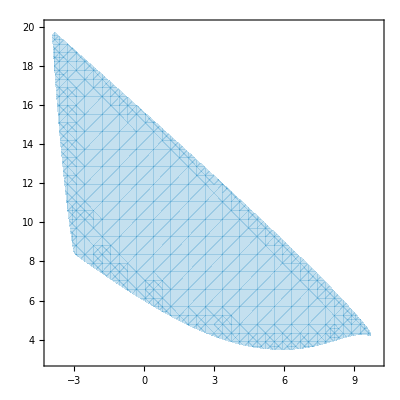
```mathematica
G=-Graphics-;
```

```mathematica
𝒪=Region[BoundaryDiscretizeGraphics[G]];
```

```mathematica
FunctionalStepperQ[Θ1_?NumberQ,W11_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,EPs,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->1000000])/.t->skip;
EPs=EquilibriumPoints[DS1];
If[AnyTrue[LSPoint/@EPs,EuclideanDistance[IC,#]<tolerance&],Return[False]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
T<MaxPeriod&&Times@@(MinMax[Table[First[σ[y1[t]+Θ1]/.S],{t,0,T,0.1}]]-0.5)<0]]
```

```mathematica
(*G2=RegionPlot[RegionMember[ℛℛ,{Θ1,W11}]&&FunctionalStepperQ[Θ1,W11],{Θ1,-4,10},{W11,3,20},(*PlotPoints->50,MaxRecursion->3,*)BoundaryStyle->None];*)
```

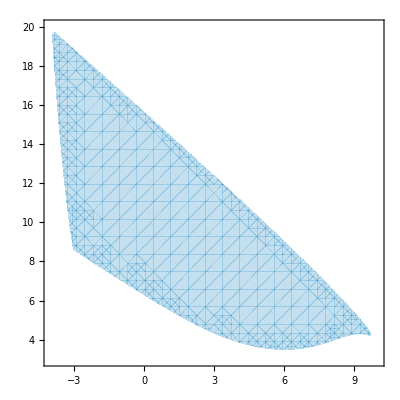
```mathematica
G2=-Graphics-;
```

```mathematica
ℱ𝒮=Region[BoundaryDiscretizeGraphics[G2]];
```

```mathematica
FunctionalStepper3Q[Θ1_?NumberQ,W11_?NumberQ,W21_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11,w21->W21},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11,w21->W21}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,EPs,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->1000000])/.t->skip;
EPs=EquilibriumPoints[DS1];
If[AnyTrue[LSPoint/@EPs,EuclideanDistance[IC,#]<tolerance&],Return[False]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->1000000];
T=S[[1,1,2,0]][[1,1,2]];
T<MaxPeriod&&Times@@(MinMax[Table[First[σ[y1[t]+Θ1]/.S],{t,0,T,0.1}]]-0.5)<0]]
```

```mathematica
$OG=Show[
ParametricPlot[{-ArcTan[(t^2-300)/(300 √3)],-(600t √3)/(t^4-600 t^2+360000)},{t,0,10 √6},PlotStyle->Directive[RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75]]],
ParametricPlot[{-ArcTan[(t √6+15)/(15 √3)],-15/(√2(t^2+5t √6+150))},{t,0,25/√6},PlotStyle->Directive[RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75]]],
ParametricPlot[{t^2/80-π/6,t/40},{t,0,4 √(5π/3)},PlotStyle->Directive[RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75]]],
Graphics[{RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75],Line[{{-ArcTan[8/(3 √3)],-(9 √2)/455},{-π/6,0}}],Line[{{π/6,(√(π/15))/2},{π/6,0}}]}],
PlotRange->All,AspectRatio->1,Frame->False,FrameStyle->Red,FrameTicks->None,Axes->False];
```

```mathematica
DisplayBodyCycle[Θ1_?NumberQ,W11_?NumberQ,SkipSteps_:1,NumSteps_:1]:=
Module[{S,PTs},
S=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[{θ1->Θ1,w11->W11},Pis],SkipSteps,NumSteps]];
If[S===$Failed,Return[$Failed]];
PTs=Map[{#[[4]],#[[5]]}&,S];
Show[
$OG,
Graphics[{Blue,AbsoluteThickness[1.5],Line[Append[PTs,First[PTs]]]}],
PlotRange->{{-0.9947592804475793,0.5235987755982991},{-0.07540269928703086,0.22882280821594225}},AspectRatio->1,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],FrameTicks->None]]
```

```mathematica
BodyCyclePeriod[Θ1_?NumberQ,W11_?NumberQ]:=
With[{GP=GaitParameters[{θ1->Θ1,w11->W11}]},
If[GP[[1]]==$Failed,Return[$Failed]];
GP[[3]]+TStar[GP[[1]],GP[[2]]]]
```

```mathematica
BodyCycleFootDown[Θ1_?NumberQ,W11_?NumberQ]:=
With[{GP=GaitParameters[{θ1->Θ1,w11->W11}]},
If[GP[[1]]==$Failed,Return[$Failed]];
GP[[1]]]
```

```mathematica
BodyCycleFootUp[Θ1_?NumberQ,W11_?NumberQ]:=
With[{GP=GaitParameters[{θ1->Θ1,w11->W11}]},
If[GP[[1]]==$Failed,Return[$Failed]];
GP[[2]]]
```

```mathematica
BodyTimeTrajectory[PSubs_:{}]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],10,1]]},
If[T===$Failed,Return[$Failed],{#[[1]],#[[4]]}&/@T]]
```

```mathematica
MotorTimeTrajectory[PSubs_:{}]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],10,1]]},
If[T===$Failed,Return[$Failed],{#[[1]],#[[2]]}&/@T]]
```

```mathematica
InterneuronTimeTrajectory[PSubs_:{}]:=
Module[{T=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[PSubs,Pis],10,1]]},
If[T===$Failed,Return[$Failed],{#[[1]],#[[3]]}&/@T]]
```